```mathematica
Quit[]
```

```mathematica
rawdata =Import["/Users/stevenschowalter/Desktop/phys191mms/HeData/mms_He_312run4.txt","Table"];
```

```mathematica
num=Dimensions[rawdata][[1]]
```

203

```mathematica
time=Take[rawdata,All,{3}];
voltage=Take[rawdata,All,{2}];
pulse=Take[rawdata,All,{1}];
```

```mathematica
temp=Table[0,{i,num}];
```

```mathematica
Do[temp[[i]]=ⅇ^(-0.004995*Log[1000*voltage[[i]]]^3+0.1314*Log[1000*voltage[[i]]]^2-1.43Log[1000*voltage[[i]]]+5.92),{i,1,num}];
```

```mathematica
timetemp=Table[0,{i,num}];
Do[timetemp[[i]]=Flatten[{time[[i]],temp[[i]]},2],{i,1,num}]
```

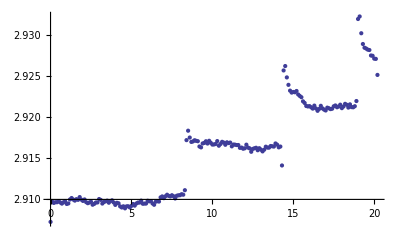

```mathematica
ListPlot[timetemp]
```

```mathematica
Q=10.5^2/1116 10^-2;
```

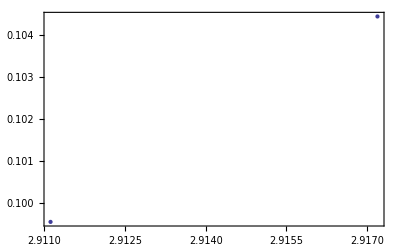

```mathematica
threshold=.002;
threshold2=.001;
dT={};
Do[If[temp[[i+1]][[1]]>temp[[i]][[1]]+threshold2,{dT=Join[dT,{{temp[[i]][[1]],Q/(-Mean[Take[temp,{i-10,i}]][[1]]+Mean[Take[temp,{i+50,i+80}]][[1]])}}]}],{i,10,num-80}]
ListPlot[dT,PlotRange->All,Frame->True]
```